```mathematica
T=ReadList["C:\Users\Коптутер\Desktop\Вариант 19.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];(*укажи свой путь к файлу*)
Det[T]
Eigenvalues[T]
Eigenvectors[T]
InterpolatingPolynomial[{2.11947*Exp[+07],1.07437*Exp[+06],-37704.5,5854.64,-1794.9,898.037,-678.477,
747.549,-1178.34,2487.06,-0.13632861880530572},x](*сюда вставляем определители, которые получились после метода гаусса, не советую в качестве проверки сравнивать с полиномом из вольфрама, он по другой сетке строит видимо, лучше строить график от получившегося полинома и искать его корни, а потом  их сравнивать с с.ч. исходной матрицы*)
```

2.11947×10^7

{10.7,9.7,8.7,7.7,6.7,5.7,4.7,3.7,2.7,1.7}

{{-1.51557×10^-9,5.15671×10^-8,-3.65134×10^-8,5.38329×10^-8,9.70631×10^-8,-1.86873×10^-7,4.07645×10^-8,1.89266×10^-7,-0.587785,0.809017},{3.12444×10^-8,-2.09523×10^-8,-9.98131×10^-8,8.77367×10^-8,-5.88812×10^-9,8.45103×10^-8,-1.84539×10^-7,-0.587785,0.654508,0.475528},{-9.72872×10^-8,3.75923×10^-8,-2.85764×10^-9,1.02149×10^-7,-1.11169×10^-7,-2.28888×10^-7,0.587786,-0.654508,-0.38471,-0.279508},{9.56396×10^-9,2.50985×10^-8,-6.55181×10^-8,1.05341×10^-7,9.60126×10^-8,-0.587785,0.654508,0.384711,0.226127,0.164291},{-4.94676×10^-8,-1.03189×10^-7,8.39284×10^-8,3.19899×10^-7,-0.587786,0.654508,0.38471,0.226127,0.132914,0.096568},{-4.97912×10^-8,-9.40526×10^-8,-2.20997×10^-7,-0.587785,0.654508,0.384711,0.226127,0.132914,0.0781251,0.0567612},{2.91091×10^-8,-3.35908×10^-8,0.587785,-0.654509,-0.38471,-0.226127,-0.132914,-0.078125,-0.0459207,-0.0333632},{-1.0167×10^-7,-0.587785,0.654509,0.38471,0.226127,0.132914,0.078125,0.0459207,0.0269915,0.0196105},{0.587786,-0.654508,-0.38471,-0.226127,-0.132914,-0.078125,-0.0459207,-0.0269915,-0.0158653,-0.0115268},{0.809017,0.475528,0.279509,0.164291,0.0965679,0.0567613,0.0333635,0.0196105,0.0115268,0.00837466}}

-0.136329+(-232.442+(10.5614+(-820.727+(141.906+(131.315+(-20.6624+(8.07673+(-1.90658+(2.64881-0.913411 (-4+x)) (-8+x)) (-5+x)) (-10+x)) (-2+x)) (-9+x)) (-3+x)) (-6+x)) (-1+x)) (-11+x)

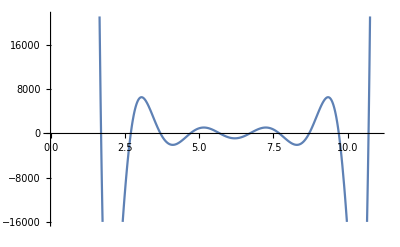

x==1.7000005113756745211030647866||x==2.6999993307878360303510012847||x==3.700000110583515981504444001||x==4.699999693066878112079274949||x==5.700000391459565542572822144||x==6.700000201636917923698233693||x==7.700000320894712597961729491||x==8.700000494007869579453719081||x==9.6999995705033129503638780401||x==10.700000375683713070419142652

```mathematica
Plot[{21194711.2837149202823638916015625-18804053.9713054038584232330322265625*(x-0)+8301275.086784250102937221527099609375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)-2428842.9710674011148512363433837890625*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)+529124.301784759736619889736175537109375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)-91365.492033982460270635783672332763671875*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)+12987.027788332930867909453809261322021484375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)-1555.66494209279744609375484287738800048828125*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)+158.985016647777541720643057487905025482177734375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)*(x-7.489999984352607498294673860073089599609375)-13.8500011005903953531515071517787873744964599609375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)*(x-7.489999984352607498294673860073089599609375)*(x-8.559999982117265204806244582869112491607666015625)+1.0000000000000011102230246251565404236316680908203125*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)*(x-7.489999984352607498294673860073089599609375)*(x-8.559999982117265204806244582869112491607666015625)*(x-9.62999997988192291131781530566513538360595703125)},{x,0,11}](*сюда и в рутс вставляй свой полином, который получился после интерполяции, лучше при выводе его из с++ в концоль или файл использовать setpercision(20)или больше, число в последней скобке поменяй с 11 до твоего самого большого собственного числа+eps*)

Roots[21194711.2837149202823638916015625-18804053.9713054038584232330322265625*(x-0)+8301275.086784250102937221527099609375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)-2428842.9710674011148512363433837890625*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)+529124.301784759736619889736175537109375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)-91365.492033982460270635783672332763671875*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)+12987.027788332930867909453809261322021484375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)-1555.66494209279744609375484287738800048828125*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)+158.985016647777541720643057487905025482177734375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)*(x-7.489999984352607498294673860073089599609375)-13.8500011005903953531515071517787873744964599609375*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)*(x-7.489999984352607498294673860073089599609375)*(x-8.559999982117265204806244582869112491607666015625)+1.0000000000000011102230246251565404236316680908203125*(x-0)*(x-1.069999997764658150600780572858639061450958251953125)*(x-2.13999999552931630120156114571727812290191650390625)*(x-3.209999993293974451802341718575917184352874755859375)*(x-4.2799999910586326024031222914345562458038330078125)*(x-5.3499999888232903089146930142305791378021240234375)*(x-6.41999998658794890360468343715183436870574951171875)*(x-7.489999984352607498294673860073089599609375)*(x-8.559999982117265204806244582869112491607666015625)*(x-9.62999997988192291131781530566513538360595703125)==0,x]
```